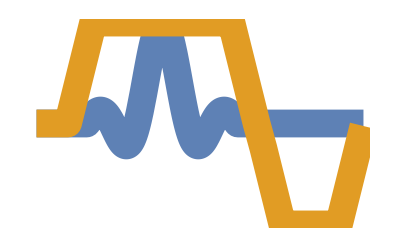

```mathematica
Plot[{Sinc[π x]UnitBox[x/6],Convolve[UnitBox[y/6.5]-UnitBox[(y-5.9)/6.5*2],UnitBox[y],y,x]},{x,-5,8},PlotStyle->Thickness[0.1/2],Axes->False,Exclusions-> None]
```

```mathematica
Rz[θ_]:={{Cos[θ],Sin[θ],0},{-Sin[θ],Cos[θ],0},{0,0,1}};p = Table[Graphics3D[{Opacity[1],ColorData[97][1],Sphere[{0,0,0},.5],Arrowheads[.15],
Opacity[Sin[2θ]^2.5+.5],Arrow[Tube[{.6Rz[4θ].{-.5,0,-1},1.2Rz[4θ].{.5,0,1}},.12]],Table[{Opacity[.2/n^(1/1.5)],Sphere[1.1Rz[4θ-.05n].{.5,0,1},.12/n^(1/6)]},{n,1,50}],Table[{Opacity[.2/n^(1/1.5)],Sphere[.6Rz[4θ-.05n].{-.5,0,-1},.12/n^(1/6)]},{n,1,50}]},Lighting->{{"Ambient", White}},Boxed->False,PlotRange->.5{{-3,3},{-3,3},{-2,3}},ViewAngle->Pi/7,ViewPoint->Front],{θ,0,2π,.1} ];
```

```mathematica
Export["Loading.gif",p,AnimationRepetitions->∞,"DisplayDurations"->1/40]
```

Loading.gif